```mathematica
Needs["FindBounce`"]
```

Potential1

```mathematica
V[phi1_,phi2_,phis_,l1_,l2_]:=-100 h^2+0.1 h^4-60 s^2+0.3 s^4+3 h^2 s^2;
minima={{0.,10.},{22.4,0.}};
```

```mathematica
bf=FindBounce[V[h,s],{h,s},minima,"MidFieldPoint"->{6.,6.}]
```

BounceFunction[<|Action -> 172.196, <<7>>, CoefficientsExtension -> {{{0.131909, 0.000144303}, {-0.464926, 0.0190419}, {-2.90688, 0.241164}, {-5.39804, 0.734216}, {-7.11279, 1.34861}, {-7.37209, 1.78776}, {-5.67688, 1.66708}, {-2.01641, 0.690625}, {2.9254, -1.13732}, <<17>>, {65.0296, -64.1162}, {95.8429, -100.369}, {105.263, -120.445}, {56.4467, -84.8858}}, <<2>>, {<<30>>}}|>]

Then we plot potential with contours, locations of minima (red points) and the final trajectory of the bounce field.

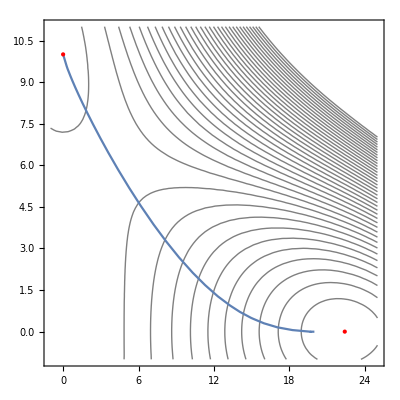

```mathematica
{rInit,rFin}=MinMax@bf["Radii"];
Show[ContourPlot[V[h,s],{h,-1,25},{s,-1,11},Contours->40,ContourShading->None,ContourStyle->Gray,Epilog->{PointSize[Large],Red,Point[minima]}],ParametricPlot[Through@bf["Bounce"][r],{r,rInit,rFin}]]
```

We can also plot the final bounce field configuration for both fields.

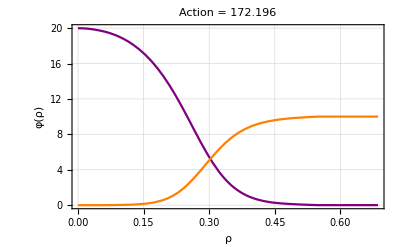

```mathematica
BouncePlot[bf,PlotLabel->Row[{"Action = ",bf["Action"]}],PlotStyle->{Purple,Orange}]
```